NDSolve::ndsz: At t == -0.494964, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 51.5223, step size is effectively zero; singularity or stiff system suspected.

-0.494964

51.5223

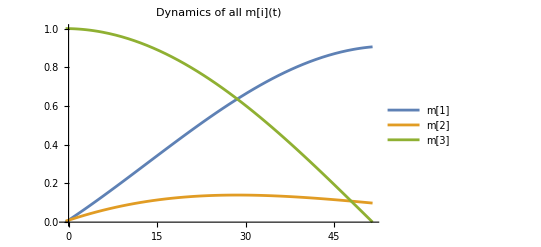

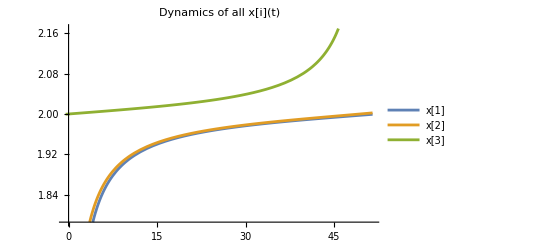

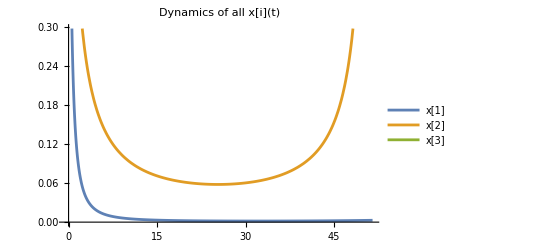

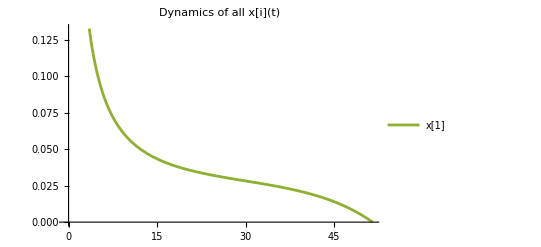

```mathematica
ClearAll["Global`*"]

u[k_,t_]:=Apply[Plus,Table[m[j][t](Abs[x[k][t]-x[j][t]]),{j,1,n}]]
ux[k_,t_]:=Apply[Plus,Table[m[j][t]( (x[k][t]-x[j][t])/Abs[x[k][t]-x[j][t]]),{j,DeleteCases[Range[1,n],k]}]]

n=3; 

(*Define initial conditions*)
initialConditions={
m[1][0]==0.01,x[1][0]==0,
m[2][0]==0.01,x[2][0]==1,
m[3][0]==1,x[3][0]==2
};

eqns=Flatten[Table[{
m[i]'[t]==-m[i][t]ux[i,t]u[i,t],
x[i]'[t]==u[i,t]^2},
{i,n}
]];

(*Solve the system numerically*)
Tstart=-2;
Tend=100;
T={t,Tstart,Tend};
sol=NDSolve[Join[eqns,initialConditions],Flatten[Table[{m[i],x[i]},{i,n}]],T];
Tstart=Apply[Max,Table[sol[[1,i,2]]["Domain"][[1,1]],{i,1,2n}]]
Tend=Apply[Min,Table[sol[[1,i,2]]["Domain"][[1,2]],{i,1,2n}]]
T={t,Tstart,Tend};

plotM=Plot[Evaluate[Table[m[i][t]/. sol,{i,n}]],T,PlotLegends->Table["m["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all m[i](t)",PlotStyle->Array[ColorData[97],n]]

plotX=Plot[Evaluate[Table[x[i][t]/. sol,{i,n}]],T,PlotLegends->Table["x["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all x[i](t)",PlotStyle->Array[ColorData[97],n]]

plotX=Plot[Evaluate[Table[x[i+1][t]-x[i][t]/. sol,{i,n}]],T,PlotLegends->Table["x["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all x[i](t)",PlotStyle->Array[ColorData[97],n]]
plotX=Plot[Evaluate[(x[2][t]-x[1][t])/(x[3][t]-x[2][t])/. sol],T,PlotLegends->Table["x["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all x[i](t)",PlotStyle->Array[ColorData[97],n]]
```